# Εργασία 3η

## 1η Άσκηση

Έστω μία τυχαία μεταβλητή Χ που ακολουθεί την κατανομή Rayleigh, με πυκνότητα πιθανότητας f(x|σ) = x/σ^2e^(x^2/(2 σ^2)), x ≥0. Να κατασκευάσετε με τη μέθοδο Neyman την ζώνη εμπιστοσύνης (condidence belt) για την παράμετρο σ ∈ [1,20] για κεντρικό διάστημα με επίπεδο εμπιστοσύνης CL = 0.9 και να την παραστήσετε γραφικά. Προτεινόμενη διαδικασία: επιλέξτε έναν ικανό αριθμό τιμών της παραμέτρου σ στο διάστημα [1, 20] και για κάθε τιμή βρείτε τα x_1(σ), x_2(σ) ώστε  ∫_0^(x_1(σ)) f(x|σ)ⅆx= (1 - CL)/2 και ∫_(x_2(σ))^(+∞) f(x|σ)ⅆx= (1 - CL)/2 (τα εν λόγω ολοκληρώματα υπολογίζονται αναλυτικά).

Λύση

```mathematica
ClearAll["Global`*"];
```

```mathematica
inches=72;
```

```mathematica
CL=0.9;
```

```mathematica
N1 = 1000;
```

```mathematica
PDF[RayleighDistribution[σ],x]
```

Piecewise[{{(ⅇ^(-x^2/(2 σ^2)) x)/σ^2, x>0}, {0, True}}]

```mathematica
f = (ⅇ^(-x^2/(2 σ^2)) x)/σ^2;
```

Παραγωγή τυχαίων, Ν1 στον αριθμό, σ:

```mathematica
sigmas = RandomReal[{1,20},N1];
```

Βρίσκουμε για κάθε τιμή τα x_1(σ), x_2(σ):

```mathematica
x1dots = ParallelTable[Quiet[Solve[Integrate[(ⅇ^(-x^2/(2 sigmas[[i]]^2)) x)/sigmas[[i]]^2,{x,0,x1}]== (1 -CL)/2 && x1>0][[1]][[1]][[2]]],{i,1,N1}];
```

```mathematica
x2dots = ParallelTable[Quiet[Solve[Integrate[(ⅇ^(-x^2/(2 sigmas[[i]]^2)) x)/sigmas[[i]]^2,{x,x2,Infinity}]== (1 -CL)/2 && x2>0][[1]][[1]][[2]]],{i,1,N1}];
```

Κατασκευάζουμε τα σημεία (σ, x_1(σ)) και (σ, x_2(σ)):

```mathematica
data1 = ParallelTable[{sigmas[[i]],x1dots[[i]]},{i,1,N1}];
```

```mathematica
data2 = ParallelTable[{sigmas[[i]],x2dots[[i]]},{i,1,N1}];
```

Πλοτάρισμα των δύο σετ σημείων:

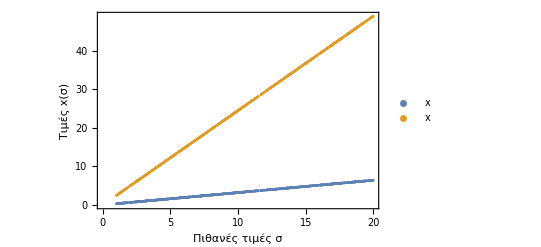

```mathematica
l1=ListPlot[{data1,data2},Frame->True,FrameLabel->{"Πιθανές τιμές σ","Τιμές x(σ)"},LabelStyle->{FontFamily->"Times New Roman",20},PlotLegends->{"x","x"}]
Export["ex1-1.png",Show[l1,ImageSize->8 inches]];
```

## 2η Άσκηση

Θεωρήστε την τυχαία μεταβλητή του προηγούμενου θέματος για σ = 10. Να παράξετε μία τυχαία τιμή αυτής της μεταβλητής, την οποία θεωρούμε ως μία μέτρηση x_obs, και στη συνέχεια να βρείτε το κεντρικό διάστημα εμπιστοσύνης με CL = 0.9 για την παράμετρο σ, χρησιμοποιώντας τη μέτρηση x_obs και τη ζώνη εμπιστοσύνης που κατασκευάσατε στο προηγούμενο θέμα. Περιλαμβάνεται η τιμή σ = 10 σε αυτό; Να επαναλάβετε τη διαδικασία 1000 φορές και να αναφέρετε το ποσοστό των διαστημάτων που δεν περιλαμβάνουν την πραγματική τιμή της παραμέτρου. Σχολιάστε το αποτέλεσμα.

Λύση

```mathematica
σ= 10;
```

Δημιουργία τυχαίου x_obs και πλοτάρισμα του:

```mathematica
xobs=RandomVariate[RayleighDistribution[σ]];
```

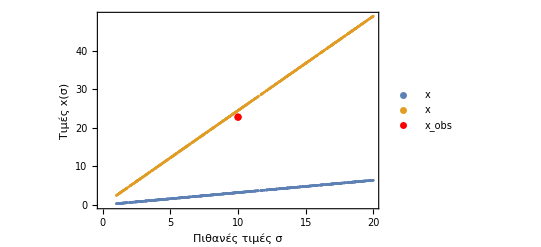

```mathematica
l2=Show[ListPlot[{data1,data2},PlotLegends->{"x","x"},Frame->True,FrameLabel->{"Πιθανές τιμές σ","Τιμές x(σ)"},LabelStyle->{FontFamily->"Times New Roman",20}],ListPlot[{{σ,xobs}},PlotStyle -> Red,PlotLegends->{"x_obs"},Frame->True,FrameLabel->{"Πιθανές τιμές σ","Τιμές x(σ)"},LabelStyle->{FontFamily->"Times New Roman",20}]]
Export["ex2-1.png",Show[l2,ImageSize->8 inches]];
```

```mathematica
Position[sigmas,_?(#==10.014767578175007&)]
```

{{551}}

```mathematica
x1dots[[551]]
```

3.20764

```mathematica
x2dots[[551]]
```

24.5136

Έλεγχος αν τα x_obs είναι εκτός ή εντός της περιοχής:

```mathematica
xobs1=RandomVariate[RayleighDistribution[σ],N1];
```

```mathematica
countsx1 = ParallelTable[Length[Position[x1dots,_?(#>xobs1[[i]]&)]],{i,1,N1}];
countsx2 = ParallelTable[Length[Position[x2dots,_?(#<xobs1[[i]]&)]],{i,1,N1}];
```

Πιθανότητα ένα σημείο να είναι μέσα στη περιοχή:

```mathematica
Percentage1 = ParallelTable[If[countsx1[[i]]==0 ,1],{i,1,N1}];
Percentage1dot=DeleteCases[Percentage1,Null];
P1 =Length[Percentage1dot]/10//N;
```

```mathematica
Percentage2 = ParallelTable[If[countsx2 [[i]]!=0,1],{i,1,N1}];
Percentage2dot=DeleteCases[Percentage2,Null];
P2=Length[Percentage2dot]/10//N;
```

```mathematica
Ptot=(P1+P2)/2
```

89.2

## 3η Άσκηση

Θεωρήστε μία τυχαία μεταβλητή που ακολουθεί κατανομή Poisson με μ = 8. Να παράξετε ένα σύνολο από Ν = 20 τιμές της τυχαίας μεταβλητής και να βρείτε την εκτίμηση μέγιστης πιθανοφάνειας για την παράμετρο μ καθώς και το σφάλμα αυτής (με την προσεγγιστική μέθοδο). Στη συνέχεια να αναφέρετε το κεντρικό διάστημα εμπιστοσύνης με CL = 0.6827 για την παράμετρο μ. Ποια είναι η απάντηση στο παραπάνω ερώτημα αν χρησιμοποιήσετε μόνο την πρώτη τιμή από το σύνολο των 20 τιμών που παράξατε;

Λύση

```mathematica
ClearAll["Global`*"];
```

```mathematica
inches=72;
N1 = 20;
CL = 0.6827;
μ1 =8;
α = 1-CL;
```

```mathematica
x = RandomVariate[PoissonDistribution[μ1],N1];
```

```mathematica
PDF[PoissonDistribution[μ],X]
```

Piecewise[{{(ⅇ^-μ μ^X)/(X!), X≥0}, {0, True}}]

Η Log Likelihood της κατανομής

```mathematica
f= LogLikelihood[PoissonDistribution[μ],x]//N
```

-200.934-20. μ+151. Log[μ]

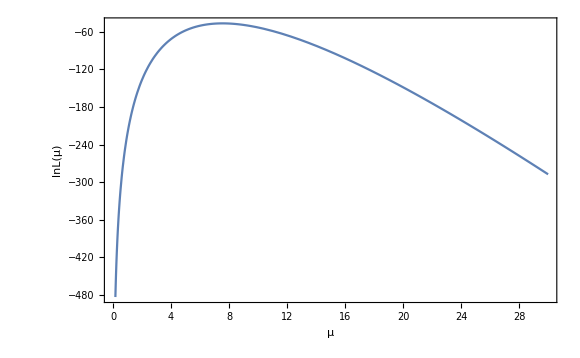

```mathematica
p1=Plot[f,{μ,0,30},Frame->True,FrameLabel->{"μ","lnL(μ)"},LabelStyle->{FontFamily->"Times New Roman",20}]
Export["ex3-1.png",Show[p1,ImageSize->8 inches]];
```

```mathematica
max ={Quiet[FindMaximum[f,μ]][[1]],Quiet[FindMaximum[f,μ]][[2]][[1]][[2]]}
```

{-46.6798,7.55}

Η Hessian της κατανομής είναι

```mathematica
μhat=μ/.Quiet[FindMaximum[f,μ][[2]]]
```

7.55

```mathematica
H = D[f,{μ ,2}]/. μ -> μhat
```

-2.64901

Έτσι το σφάλμα της εκτίμησης προσεγγιστικά είναι:

```mathematica
Subscript[σ, μ]=Sqrt[-H]^(-1)
```

0.61441

Κεντρικά διαστήματα για τη μέση τιμή κατανομής Poisson

```mathematica
μup=NumberForm[1/2*InverseCDF[ChiSquareDistribution[2*(N1+1)],1-α ],3]
```

22.9

```mathematica
μlow =NumberForm[1/2*InverseCDF[ChiSquareDistribution[2*N1],α],3]
```

17.6

Το ίδιο για μία τιμή:

Η Log Likelihood της κατανομής

```mathematica
f1= LogLikelihood[PoissonDistribution[μ],{x[[1]]}]//N
```

-10.6046-1. μ+8. Log[μ]

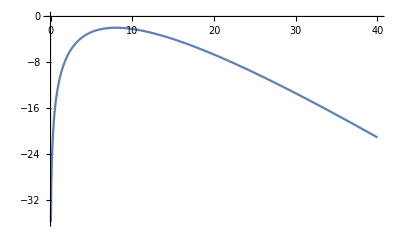

```mathematica
Plot[f1,{μ,0,40}]
```

```mathematica
max1 ={Quiet[FindMaximum[f1,μ]][[1]],Quiet[FindMaximum[f1,μ]][[2]][[1]][[2]]}
```

{-1.96907,8.}

Η Hessian της κατανομής είναι

```mathematica
μhat1=μ/.Quiet[FindMaximum[f1,μ][[2]]]
```

8.

```mathematica
H1 = D[f1,{μ ,2}]/. μ -> μhat1
```

-0.125

Έτσι το σφάλμα της εκτίμησης προσεγγιστικά είναι:

```mathematica
Subscript[σ1, μ]=Sqrt[-H1]^(-1)
```

2.82843

Κεντρικά διαστήματα για τη μέση τιμή κατανομής Poisson

```mathematica
μup=NumberForm[1/2*InverseCDF[ChiSquareDistribution[2*(1+1)],1-α ],3]
```

2.36

```mathematica
μlow =NumberForm[1/2*InverseCDF[ChiSquareDistribution[2*1],α],3]
```

0.382

## 4η Άσκηση

Θεωρήστε μία τυχαία μεταβλητή X που ακολουθεί κανονική κατανομή X ∼ N(μ = 30, σ = 1). Να παράξετε ένα σύνολο Σ από k = 5,20,50 ανεξάρτητες μετρήσεις της μεταβλητής . Θεωρώντας άγνωστες τις παραμέτρους της κατανομής, να αναφέρετε τα κεντρικά διαστήματα εμπιστοσύνης με CL = 0.6827 για την εκτίμηση αυτών. Να επαναλάβετε τη διαδικασία για 1000 τυχαία σύνολα ( x̄, s είναι ο αριθμητικός μέσος και η διασπορά, αντίστοιχα, του συνόλου Σ):

να δείξετε σε ιστόγραμμα την κατανομή της ποσότητας (√k( x̄ - μ))/s για τα 1000 τυχαία σύνολα,

να δείξετε σε ιστόγραμμα την κατανομή της ποσότητας ((k-1)s^2)/σ^2 για τα 1000 τυχαία σύνολα,

να αναφέρετε το ποσοστό των διαστημάτων εμπιστοσύνης που περιέχουν τις πραγματικές τιμές των παραμέτρων της κατανομής.

Λύση

```mathematica
ClearAll["Global`*"];
```

```mathematica
inches=72;
k={5,20,50};
μ = 30;
σ = 1;
CL = 0.6827;
N1 = 1000;
```

Παράγουμε τυχαίους k μεταβλητές:

```mathematica
Σ1s = ParallelTable[RandomVariate[NormalDistribution[μ,σ],k[[1]]],{i,1,N1}];
Σ2s = ParallelTable[RandomVariate[NormalDistribution[μ,σ],k[[2]]],{i,1,N1}];
Σ3s = ParallelTable[RandomVariate[NormalDistribution[μ,σ],k[[3]]],{i,1,N1}];
```

Υπολογίζουμε τη ποσότητα του α ερωτήματος

```mathematica
fraq1= ParallelTable[Sqrt[k[[1]]]*(Mean[Σ1s[[i]]] - μ)/StandardDeviation[Σ1s[[i]]],{i,1,N1}];
fraq2= ParallelTable[Sqrt[k[[2]]]*(Mean[Σ2s[[i]]] - μ)/StandardDeviation[Σ2s[[i]]],{i,1,N1}];
fraq3= ParallelTable[Sqrt[k[[3]]]*(Mean[Σ3s[[i]]] - μ)/StandardDeviation[Σ3s[[i]]],{i,1,N1}];
```

Ιστόγραμμα της ποσότητας για κάθε k

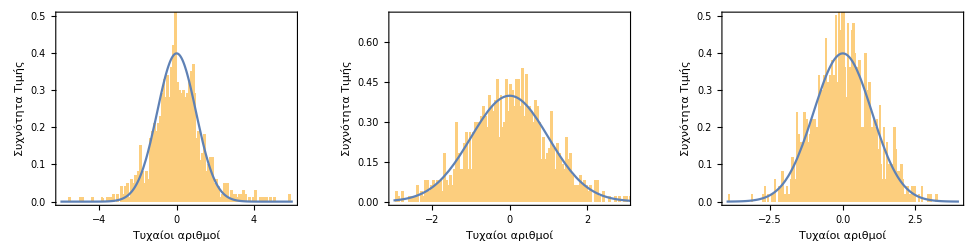

```mathematica
h1 = Show[{Histogram[fraq1,200,"PDF",Frame->True,FrameLabel->{"Τυχαίοι αριθμοί","Συχνότητα Τιμής"},LabelStyle->{FontFamily->"Times New Roman",20},PlotRange->{{-6,6},{0,0.5}}],Plot[PDF[NormalDistribution[],x],{x,-6,6}]}];
h2 =Show[{ Histogram[fraq2,200,"PDF",Frame->True,FrameLabel->{"Τυχαίοι αριθμοί","Συχνότητα Τιμής"},LabelStyle->{FontFamily->"Times New Roman",20},PlotRange->{{-3,3},{0,0.7}}],Plot[PDF[NormalDistribution[],x],{x,-3,4}]}];
h3 = Show[{Histogram[fraq3,200,"PDF",Frame->True,FrameLabel->{"Τυχαίοι αριθμοί","Συχνότητα Τιμής"},LabelStyle->{FontFamily->"Times New Roman",20},PlotRange->{{-4,4},{0,0.5}}],Plot[PDF[NormalDistribution[],x],{x,-4,4}]}];
g1=GraphicsRow[{h1,h2,h3}]
Export["ex4-1.png",Show[g1,ImageSize->15 inches]];
```

Υπολογίζουμε τη ποσότητα του b ερωτήματος

```mathematica
fraq1dot= ParallelTable[Sqrt[k[[1]]]*StandardDeviation[Σ1s[[i]]]^2/σ ^2,{i,1,N1}];
fraq2dot= ParallelTable[Sqrt[k[[2]]]*StandardDeviation[Σ2s[[i]]]^2/σ ^2,{i,1,N1}];
fraq3dot= ParallelTable[Sqrt[k[[3]]]*StandardDeviation[Σ3s[[i]]]^2/σ ^2,{i,1,N1}];
```

Ιστόγραμμα της ποσότητας για κάθε k

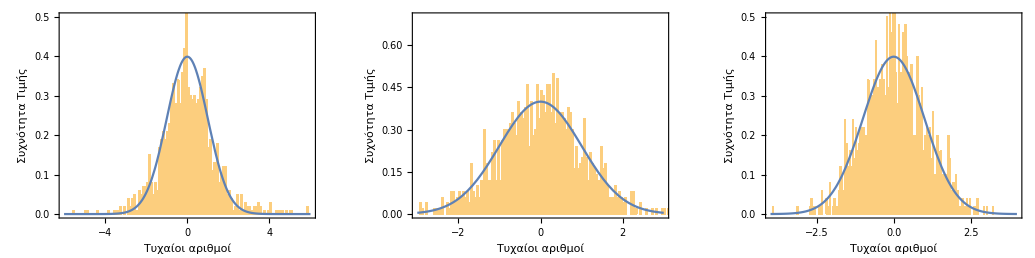

```mathematica
h1dot = Show[{Histogram[fraq1,200,"PDF",Frame->True,FrameLabel->{"Τυχαίοι αριθμοί","Συχνότητα Τιμής"},LabelStyle->{FontFamily->"Times New Roman",20},PlotRange->{{-6,6},{0,0.5}}],Plot[PDF[NormalDistribution[],x],{x,-6,6}]}];
h2dot =Show[{ Histogram[fraq2,200,"PDF",Frame->True,FrameLabel->{"Τυχαίοι αριθμοί","Συχνότητα Τιμής"},LabelStyle->{FontFamily->"Times New Roman",20},PlotRange->{{-3,3},{0,0.7}}],Plot[PDF[NormalDistribution[],x],{x,-3,3}]}];
h3dot = Show[{Histogram[fraq3,200,"PDF",Frame->True,FrameLabel->{"Τυχαίοι αριθμοί","Συχνότητα Τιμής"},LabelStyle->{FontFamily->"Times New Roman",20},PlotRange->{{-4,4},{0,0.5}}],Plot[PDF[NormalDistribution[],x],{x,-4,4}]}];
g2=GraphicsRow[{h1dot,h2dot,h3dot}]
Export["ex4-2.png",Show[g2,ImageSize->15 inches]];
```

Υπολογισμός ποσοστών των διαστημάτων εμπιστοσύνης

Διασπορά

```mathematica
σmin1= ParallelTable[Sqrt[(k[[1]]-1)*StandardDeviation[Σ1s[[i]]]^2/(InverseCDF[ChiSquareDistribution[(k[[1]]-1)],(1-CL)/2])],{i,1,N1}];
σmin2= ParallelTable[Sqrt[(k[[2]]-1)*StandardDeviation[Σ2s[[i]]]^2/(InverseCDF[ChiSquareDistribution[(k[[2]]-1)],(1-CL)/2])],{i,1,N1}];
σmin3= ParallelTable[Sqrt[(k[[3]]-1)*StandardDeviation[Σ3s[[i]]]^2/(InverseCDF[ChiSquareDistribution[(k[[3]]-1)],(1-CL)/2])],{i,1,N1}];
```

```mathematica
σmax1= ParallelTable[Sqrt[(k[[1]]-1)*StandardDeviation[Σ1s[[i]]]^2/(InverseCDF[ChiSquareDistribution[(k[[1]]-1)],1- (1-CL)/2])],{i,1,N1}];
σmax2= ParallelTable[Sqrt[(k[[2]]-1)*StandardDeviation[Σ2s[[i]]]^2/(InverseCDF[ChiSquareDistribution[(k[[2]]-1)],1- (1-CL)/2])],{i,1,N1}];
σmax3= ParallelTable[Sqrt[(k[[3]]-1)*StandardDeviation[Σ3s[[i]]]^2/(InverseCDF[ChiSquareDistribution[(k[[3]]-1)],1- (1-CL)/2])],{i,1,N1}];
```

```mathematica
Counts1= ParallelTable[If[σ >=σmin1[[i]],1,0],{i,1,N1}];
Counts11 = ParallelTable[If[σ <=σmax1[[i]],1,0],{i,1,N1}]; 
Counts2= ParallelTable[If[σ >=σmin2[[i]],1,0],{i,1,N1}];
Counts22 = ParallelTable[If[ σ <=σmax2[[i]],1,0],{i,1,N1}]; 
Counts3= ParallelTable[If[σ >=σmin3[[i]] ,1,0],{i,1,N1}];
Counts33= ParallelTable[If[ σ <=σmax3[[i]],1,0],{i,1,N1}];
```

```mathematica
Counts1dot = ParallelTable[If[Counts1[[i]]==Counts11[[i]],1],{i,1,N1}]; 
Counts2dot = ParallelTable[If[Counts2[[i]]==Counts22[[i]],1],{i,1,N1}]; 
Counts3dot = ParallelTable[If[Counts3[[i]]==Counts33[[i]],1],{i,1,N1}];
```

Πιθανότητες:

```mathematica
Percentage1=DeleteCases[Counts1dot,Null];
Percentage2=DeleteCases[Counts2dot,Null];
Percentage3=DeleteCases[Counts3dot,Null];
P1 =Length[Percentage1]/10//N
P2 =Length[Percentage2]/10//N
P3 =Length[Percentage3]/10//N
```

67.

67.4

68.5

Μέση τιμή

Διασπορά

```mathematica
μmin1= ParallelTable[Mean[Σ1s[[i]]] -Abs[InverseCDF[StudentTDistribution[k[[1]]-1],(1-CL)/2]]*StandardDeviation[Σ1s[[i]]]/Sqrt[k[[1]]] ,{i,1,N1}];
μmin2= ParallelTable[Mean[Σ2s[[i]]] -Abs[InverseCDF[StudentTDistribution[k[[2]]-1],(1-CL)/2]]*StandardDeviation[Σ2s[[i]]]/Sqrt[k[[2]]],{i,1,N1}];
μmin3= ParallelTable[Mean[Σ3s[[i]]] -Abs[InverseCDF[StudentTDistribution[k[[3]]-1],(1-CL)/2]]*StandardDeviation[Σ3s[[i]]]/Sqrt[k[[3]]],{i,1,N1}];
```

```mathematica
μmax1= ParallelTable[Mean[Σ1s[[i]]] +Abs[InverseCDF[StudentTDistribution[k[[1]]-1],(1-CL)/2]]*StandardDeviation[Σ1s[[i]]]/Sqrt[k[[1]]] ,{i,1,N1}];
μmax2= ParallelTable[Mean[Σ2s[[i]]] +Abs[InverseCDF[StudentTDistribution[k[[2]]-1],(1-CL)/2]]*StandardDeviation[Σ2s[[i]]]/Sqrt[k[[2]]],{i,1,N1}];
μmax3= ParallelTable[Mean[Σ3s[[i]]] +Abs[InverseCDF[StudentTDistribution[k[[3]]-1],(1-CL)/2]]*StandardDeviation[Σ3s[[i]]]/Sqrt[k[[3]]],{i,1,N1}];
```

```mathematica
Counts1μ= ParallelTable[If[μ >=μmin1[[i]],1,0],{i,1,N1}];
Counts11μ = ParallelTable[If[μ <=μmax1[[i]],1,0],{i,1,N1}];
Counts2μ= ParallelTable[If[μ >=μmin2[[i]],1,0],{i,1,N1}];
Counts22μ = ParallelTable[If[ μ <=μmax2[[i]],1,0],{i,1,N1}]; 
Counts3μ= ParallelTable[If[μ >=μmin3[[i]] ,1,0],{i,1,N1}];
Counts33μ= ParallelTable[If[ μ <=μmax3[[i]],1,0],{i,1,N1}];
```

```mathematica
Counts1dotμ = ParallelTable[If[Counts1μ[[i]]==Counts11μ[[i]],1],{i,1,N1}];
Counts2dotμ = ParallelTable[If[Counts2μ[[i]]==Counts22μ[[i]],1],{i,1,N1}]; 
Counts3dotμ = ParallelTable[If[Counts3μ[[i]]==Counts33μ[[i]],1],{i,1,N1}];
```

Πιθανότητες:

```mathematica
Percentage1μ=DeleteCases[Counts1dotμ,Null];
Percentage2μ=DeleteCases[Counts2dotμ,Null];
Percentage3μ=DeleteCases[Counts3dotμ,Null];
P1μ =Length[Percentage1μ]/10//N
P2μ =Length[Percentage2μ]/10//N
P3μ =Length[Percentage3μ]/10//N
```

68.5

68.3

69.3

## 5η Άσκηση

Το φροντιστήριο Α είχε 40 μαθητές Γ΄ Λυκείου, από τους οποίους οι 30 πέτυχαν στις Πανελλαδικές εξετάσεις. Το φροντιστήριο Β είχε 200 μαθητές από τους οποίους πέτυχαν οι 130. Ποια είναι τα διαστήματα εμπιστοσύνης (μέθοδοι Wilson και Clopper-Pearson) με CL = 0.95 για το ποσοστό επιτυχίας κάθε φροντιστηρίου; Θεωρήστε ότι ο αριθμός των επιτυχόντων ακολουθεί διωνυμική κατανομή με κάποια πιθανότητα p. Ποιο από τα δύο φροντιστήρια θα εμπιστευόσασταν περισσότερο; Αν την επόμενη χρονιά το φροντιστήριο Β έχει 180 μαθητές, μπορείτε να προβλέψετε (κεντρική τιμή και σφάλμα με CL = 68.27%) τον αριθμό αυτών που θα πετύχουν;

Λύση

```mathematica
ClearAll["Global`*"];
```

```mathematica
inches=72;
CL = 0.95;
nA = 40;
xA = 30;
nB = 200;
xB = 130;
```

Μέθοδος Clopper - Pearson:

Φροντιστήριο Α:

```mathematica
p1A = (xA*InverseCDF[FRatioDistribution[2xA,2(nA-xA+1)],1-CL])/(nA - xA +1 + xA*InverseCDF[FRatioDistribution[2xA,2(nA-xA+1)],1-CL])
```

0.61294

```mathematica
p2A = ((xA+1)*InverseCDF[FRatioDistribution[2(xA+1),2(nA-xA)],CL])/(nA - xA +( xA+1)*InverseCDF[FRatioDistribution[2(xA+1),2(nA-xA)],CL])
```

0.85763

Φροντιστήριο Β:

```mathematica
p1B = (xB*InverseCDF[FRatioDistribution[2xB,2(nB-xB+1)],1-CL])/(nB - xB +1 + xB*InverseCDF[FRatioDistribution[2xB,2(nB-xB+1)],1-CL])
```

0.59061

```mathematica
p2B = ((xB+1)*InverseCDF[FRatioDistribution[2(xB+1),2(nB-xB)],CL])/(nB - xB +( xB+1)*InverseCDF[FRatioDistribution[2(xB+1),2(nB-xB)],CL])
```

0.706024

Μέθοδος Wilson:

```mathematica
z =InverseCDF[NormalDistribution[0,1],(1-CL)/2]
```

-1.95996

Φροντιστήριο Α:

```mathematica
p1 =xA/nA ;
```

```mathematica
pWA1 = (p1+ z^2/(2nA))/(1+z^2/(2nA))+ z/(1 +  z^2/nA)Sqrt[p1(1-p1)/nA + z^2/(4nA^2)]
```

0.63142

```mathematica
pWA2= (p1+ z^2/(2nA))/(1+z^2/(2nA))- z/(1 +  z^2/nA)Sqrt[p1(1-p1)/nA + z^2/(4nA^2)]
```

0.891489

Φροντιστήριο Β:

```mathematica
p2 =xB/nB ;
```

```mathematica
pWB1 = (p2+ z^2/(2nB))/(1+z^2/(2nB))+ z/(1 +  z^2/nB)Sqrt[p1(1-p1)/nB + z^2/(4nB^2)]
```

0.5937

```mathematica
pWB2= (p1+ z^2/(2nB))/(1+z^2/(2nB))- z/(1 +  z^2/nB)Sqrt[p1(1-p1)/nB + z^2/(4nB^2)]
```

0.812008

Ποιο να προτιμήσουμε;

```mathematica
Grid[{{"Φροντιστήριο","Πιθανότητα","Clopper-Pearson","Wilson"},{"A",p1 //N,{p1A ,p2A},{pWA1,pWA2}},{"B",p2//N ,{p1B ,p2B},{pWB1,pWB2}}},Frame->All]
```

Φροντιστήριο | Πιθανότητα | Clopper-Pearson | Wilson
A | 0.75 | {0.61294,0.85763} | {0.63142,0.891489}
B | 0.65 | {0.59061,0.706024} | {0.5937,0.812008}

Με χρήση της διωνυμικής κατανομής:

```mathematica
pA=Probability[x==30,x\[Distributed]BinomialDistribution[40,0.75]]//N
```

0.144364

```mathematica
pB=Probability[x==130,x\[Distributed]BinomialDistribution[200,0.75]]//N
```

0.000418365

Αριθμός επιτυχόντων για το φροντιστήριο Β:

```mathematica
nBdot = 180;
CL1 = 0.6827;
```

```mathematica
xBdot=Expectation[x,x\[Distributed]BinomialDistribution[nBdot,p2]]
```

117

Φροντιστήριο Β:

```mathematica
p1Bdot = (xBdot*InverseCDF[FRatioDistribution[2*xBdot,2(nBdot-xBdot+1)],1-CL1])/(nBdot - xBdot +1 + xBdot*InverseCDF[FRatioDistribution[2xBdot,2(nBdot-xBdot+1)],1-CL1])
```

0.629926

```mathematica
p2Bdot = ((xBdot+1)*InverseCDF[FRatioDistribution[2(xBdot+1),2(nBdot-xBdot)],CL1])/(nBdot - xBdot +( xBdot+1)*InverseCDF[FRatioDistribution[2(xBdot+1),2(nBdot-xBdot)],CL1])
```

0.669206

Άρα το εύρος επιτυχόντων είναι:

```mathematica
nmin=NumberForm[p1Bdot*nBdot,3]
```

113.

```mathematica
nmax=NumberForm[p2Bdot*nBdot,3]
```

120.